```mathematica
coefs={0.1148111411606187,-1.0890359818095612,-0.0001315041128850,0.0343835957550578,0.0004291938372718,-0.0027365026444149,0.0000036250608633,-0.0006158985762478,-0.0001194537270706,-0.0001609937576612,0.0000352049846098,0.0015369009785501,-0.0001760873815461,-0.0022414443517882,-0.0000409720318506,0.0022012696303875,-0.0002471099665046,-0.0009447696842387,0.0003133801814491,-0.0002404099308919,-0.0003606248503112,0.0007178656778018,0.0007204516398194,-0.0003202061328416,-0.0006151105369743,-0.0005122282321663,0.0002754189429771,0.0008263778570974,-0.0002608986059040,0.0000301198121147,-0.0000493108435312,-0.0003831355753713,-0.0003038853044169,0.0004347819957462,0.0001628534150194,0.0001121706378524,-0.0004581840065801,-0.0005398921367449,-0.0000486230796984,0.0008347062571416,-0.0002383690941223,-0.0002300169571638,-0.0002340863420734,0.0001875168054469,0.0001065394801738,0.0000982659171714,-0.0001050690820931,0.0001734269340133,0.0002993335425389,-0.0004186125039484,0.0002223920852461,-0.0001027629859754};
```

```mathematica
TaylorApprox[coefs_][x_]:=Sum[coefs[[i+1]]*Sin[i*x], {i, 0,Length[coefs]-1}]
IntegralLoss[f_]:=NIntegrate[(Sin[x]-f[f[x]])^2, {x, 0, 2Pi}]
```

```mathematica
approx=TaylorApprox[coefs];
```

```mathematica
IntegralLoss[approx]
```

6.92714×10^-6

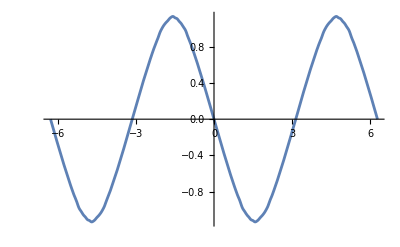

```mathematica
Plot[approx[x], {x, -2Pi, 2Pi}]
```

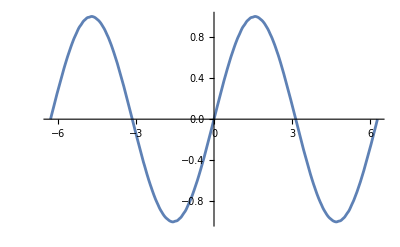

```mathematica
Plot[approx[approx[x]], {x, -2Pi, 2Pi}]
```

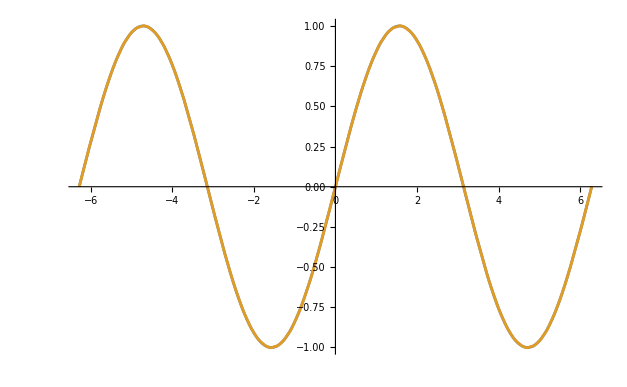

```mathematica
Plot[{Sin[x], approx[approx[x]]}, {x, -2Pi, 2Pi}]
```